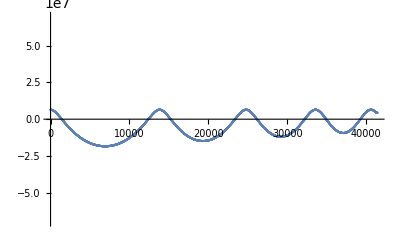

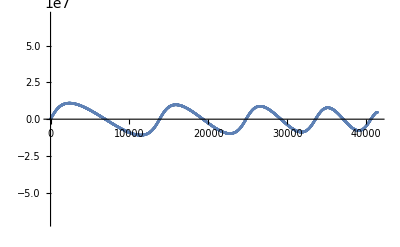

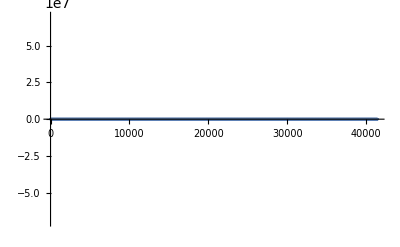

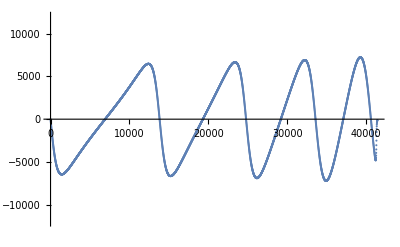

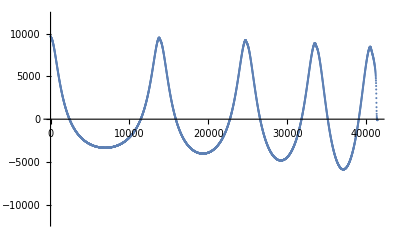

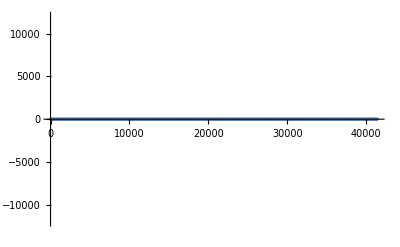

agora os plots do projeto 2

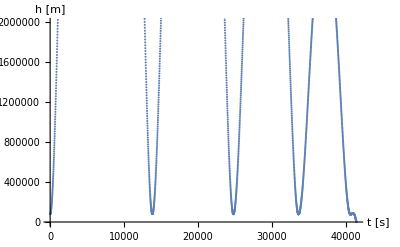

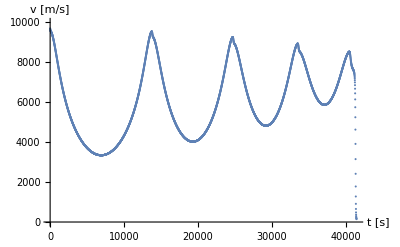

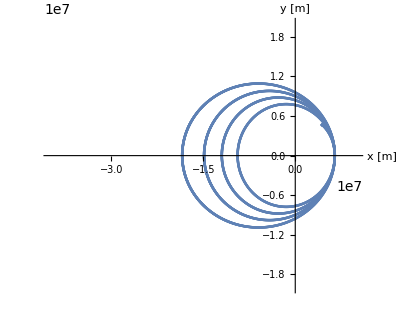

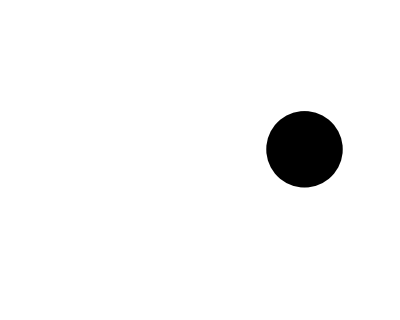

-Graphics-

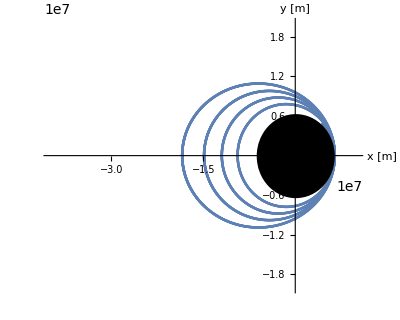

```mathematica
data=Import["/run/media/pedro/work/Documents/bbAula_pedro/aaaFisicaComputacionalTakeII /avaliar_projeto2/Solucao_projeto2/g0p2c1_out.txt", "Table"];
TableForm[data];

ListPlot[ data[[All,{1,2}]], PlotRange->{All,{-70000000,70000000}}]
ListPlot[ data[[All,{1,3}]], PlotRange->{All,{-70000000,70000000}}]
ListPlot[ data[[All,{1,4}]], PlotRange->{All,{-70000000,70000000}}]
ListPlot[ data[[All,{1,5}]], PlotRange->{All,{-12000,12000}}]
ListPlot[ data[[All,{1,6}]], PlotRange->{All,{-12000,12000}}]
ListPlot[ data[[All,{1,7}]], PlotRange->{All,{-12000,12000}}]

Print["agora os plots do projeto 2"];

ListPlot[ data[[All,{1,8}]], AxesLabel->{"t [s]","h [m]"}, AxesLabel->{"x [m]","y [m]"}, PlotRange->{All,{000,2000000}}]
ListPlot[ data[[All,{1,9}]], AxesLabel->{"t [s]","v [m/s]"}, PlotRange->{All,{000,10000}}]

fig1=ListPlot[ data[[All,{2,3}]], AxesLabel->{"x [m]","y [m]"}, PlotRange->{{-40000000,10000000},{-20000000,20000000}}, AspectRatio->4/5]

fig2=Graphics[Disk[{0,0},6371000], AxesLabel->{"x [m]","y [m]"}, PlotRange->{{-40000000,10000000},{-20000000,20000000}}, AspectRatio->4/5]

fig2=Graphics[Disk[{0,0},6371000], AxesLabel->{"x [m]","y [m]"}, PlotRange->{{-40000000,10000000},{-20000000,20000000}}, AspectRatio->4/5]

Show[fig1,fig2]
```

Velocidade da órbita circular e velocidade de escape

```mathematica
G=6.674*10^(-11);
Mt=5.972*10^(+24);
Rt=6.371*10^(+6);
vcir=Sqrt[ G *Mt/Rt]
vesc=Sqrt[ 2* G *Mt/Rt]
```

7909.5

11185.7